### What fraction within patterns are reused

### Single path dependency

### Correcting year dependencies

### Gallery plot for bounding box

### What fraction of new patterns depend on elements of old patterns?

### Dependency matrix

```mathematica
$LifeParts
```

```mathematica
Head[$LifeParts]
```

Association

```mathematica
Keys[$LifeParts]
```

{Oscillator,Spaceship,Strict still life,Gun,Puffer,Induction coil,Reflector}

```mathematica
[[1]]
```

{1970,1971}

```mathematica
mat=Boole[Outer[SubsetQ[#2,#1]&,
Values[$LifeParts["Oscillator"]],
Values[$LifeParts["Oscillator"]],
1]];
```

```mathematica
matdiff = ReplacePart[mat, Thread[Table[{i, i}, {i, Length[mat]}]-> 0]];
```

```mathematica
ArrayPlot[matdiff]
```

-Graphics-

```mathematica
diffs = DeleteCases[Position[mat,1],{x_,x_}];
```

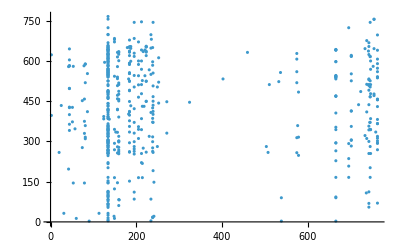

```mathematica
ListPlot[diffs]
```

```mathematica
TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 10]
```

{134,184,665,762,159,742,195,156,745,238}

```mathematica
Values[$LifeParts["Oscillator"]][[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 10]]]
```

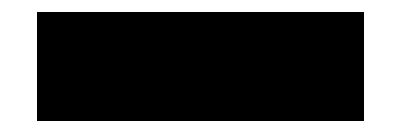
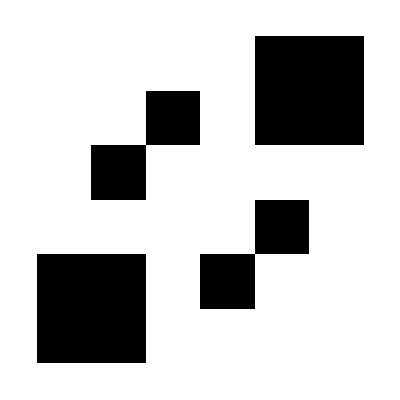
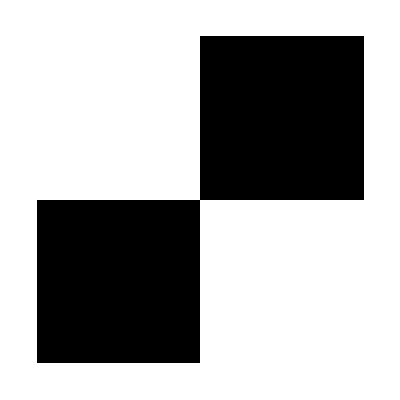
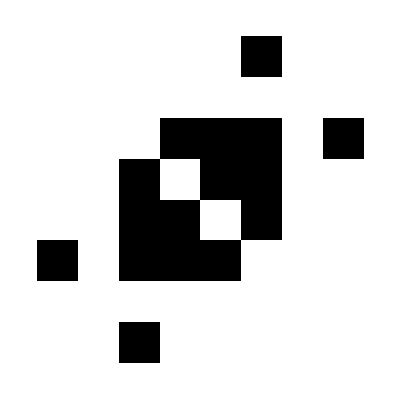
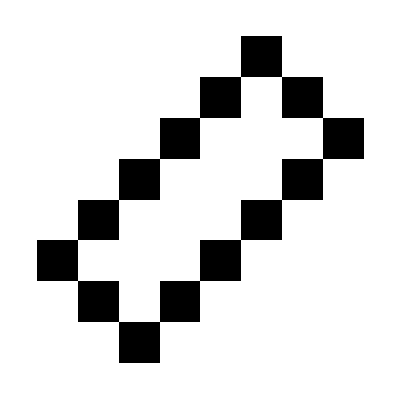
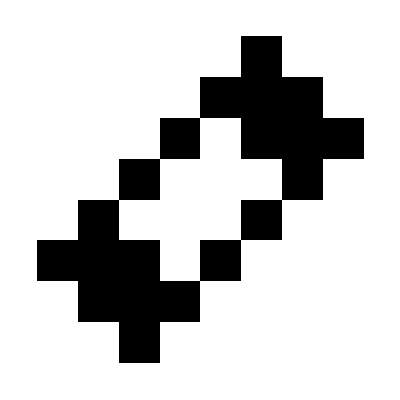
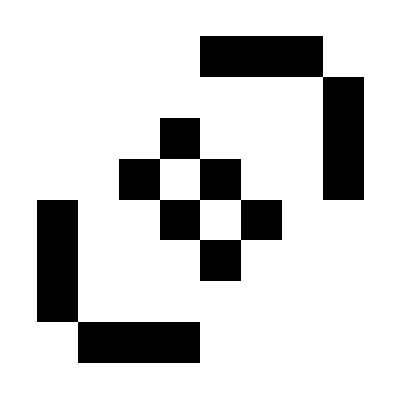
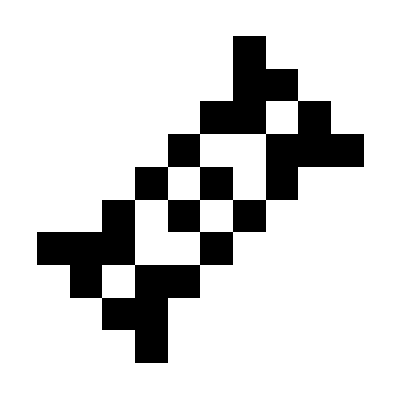

```mathematica
Column[Map[ArrayPlot, Values[$LifeParts["Oscillator"]][[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 10]]], {2}]]
```

```mathematica
TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 2][[{2}]]
```

{184}

```mathematica
Fold[.8 #+#2&,Values[$LifeParts["Oscillator"]][[184]]]
```

Thread::tdlen: Objects of unequal length in {{0.,0.,0.,0.8,1.44,1.44},{0.,0.,0.64,0.8,1.44,1.44},{0.,0.64,0.,0.8,0.8,0.8},{«1»},{1.44,1.44,0.8,0.64,0.,0.},{1.44,1.44,0.8,0.,0.,0.}}+{«1»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

$Aborted

```mathematica
MapThread[If[#2==1,-1,#]&, {Fold[.8 #+#2&,#], Last[#]}, 2]&/@Values[$LifeParts["Oscillator"]][[{184}]]
```

Thread::tdlen: Objects of unequal length in {{0.,0.,0.,0.8,1.44,1.44},{0.,0.,0.64,0.8,1.44,1.44},{0.,0.64,0.,0.8,0.8,0.8},{«1»},{1.44,1.44,0.8,0.64,0.,0.},{1.44,1.44,0.8,0.,0.,0.}}+{«1»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

```mathematica
ArrayPlot[
With[{u=
#},MapThread[If[#2==1,-1,#]&,{Fold[.8 #+#2&,u],Last[u]},2]]]&/@Values[$LifeParts["Oscillator"]][[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 10]]]
```

Thread::tdlen: Objects of unequal length in {{0.,0.,0.,0.8,1.44,1.44},{0.,0.,0.64,0.8,1.44,1.44},{0.,0.64,0.,0.8,0.8,0.8},{«1»},{1.44,1.44,0.8,0.64,0.,0.},{1.44,1.44,0.8,0.,0.,0.}}+{«1»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

$Aborted

```mathematica
ArrayPlot/@#&/@Values[$LifeParts["Oscillator"]][[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 10]]]
```

{{-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Values[$LifeParts["Oscillator"]][[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 2][[2]]]]
```

{{{0,0,0,0,1,1},{0,0,1,0,1,1},{0,1,0,0,0,0},{0,0,0,0,1,0},{1,1,0,1,0,0},{1,1,0,0,0,0}},{{0,0,0,1,1,1},{0,0,0,1,1,1},{0,0,0,1,1,1},{1,1,1,0,0,0},{1,1,1,0,0,0},{1,1,1,0,0,0}},{{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0},{0,0,0,1,1,1,0,1},{0,0,1,0,1,1,0,0},{0,0,1,1,0,1,0,0},{1,0,1,1,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0}},{{0,0,0,0,0,1,0,0},{0,0,0,0,1,0,1,0},{0,0,0,1,0,0,0,1},{0,0,1,0,0,0,1,0},{0,1,0,0,0,1,0,0},{1,0,0,0,1,0,0,0},{0,1,0,1,0,0,0,0},{0,0,1,0,0,0,0,0}},{{0,0,0,0,0,1,0,0},{0,0,0,0,1,1,1,0},{0,0,0,1,0,1,1,1},{0,0,1,0,0,0,1,0},{0,1,0,0,0,1,0,0},{1,1,1,0,1,0,0,0},{0,1,1,1,0,0,0,0},{0,0,1,0,0,0,0,0}},{{0,0,0,0,1,1,1,0},{0,0,0,0,0,0,0,1},{0,0,0,1,0,0,0,1},{0,0,1,0,1,0,0,1},{1,0,0,1,0,1,0,0},{1,0,0,0,1,0,0,0},{1,0,0,0,0,0,0,0},{0,1,1,1,0,0,0,0}},{{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,1,1,0,1,0},{0,0,0,0,1,0,0,1,1,1},{0,0,0,1,0,1,0,1,0,0},{0,0,1,0,1,0,1,0,0,0},{1,1,1,0,0,1,0,0,0,0},{0,1,0,1,1,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0}},{{0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,1},{0,0,0,0,1,0,0,0,0,1},{0,0,0,1,0,1,0,1,0,0},{0,0,1,0,1,0,1,0,0,0},{1,0,0,0,0,1,0,0,0,0},{1,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0}}}

```mathematica
ArrayPlot[Values[$LifeParts["Oscillator"]][[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 2]][[2]][[1]]]]
```

$Aborted

```mathematica
ArrayPlot[Values[$LifeParts["Oscillator"]][[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 2][[2]]]][[1]]]
```

-Graphics-

```mathematica
Values[$LifeParts["Oscillator"]][[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 2][[2]]]] // Length
```

8

```mathematica
ArrayPlot/@Values[$LifeParts["Oscillator"]][[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 10]]][[-3]]
```

{-Graphics-}

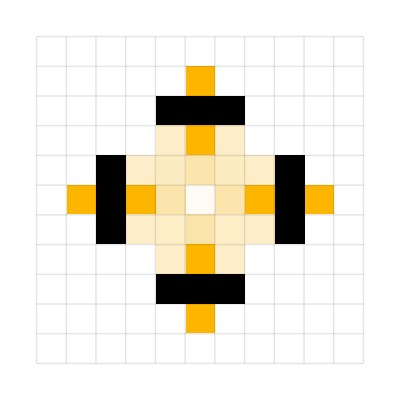

```mathematica
CellularAutomatonHistoryPlot["GameOfLife", {Values[$LifeParts["Oscillator"]][[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 10]]][[3]][[2]],0}, 17]
```

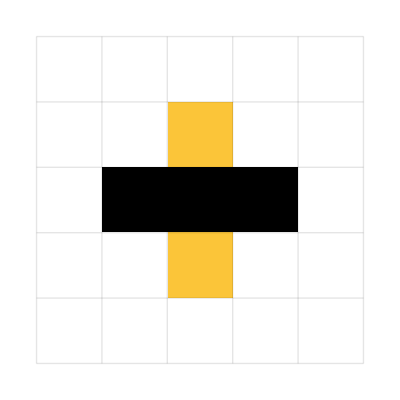
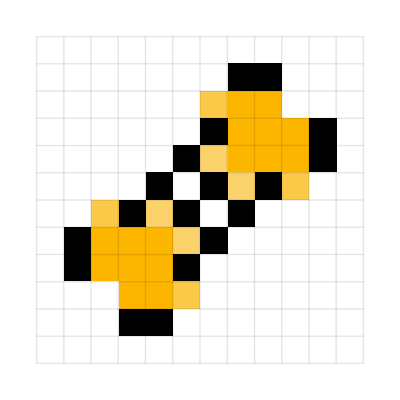
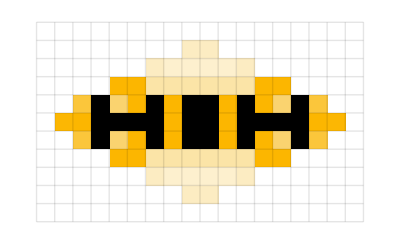
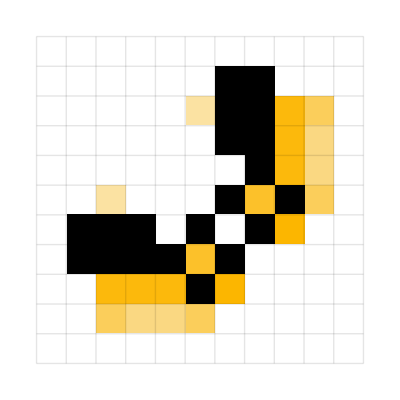
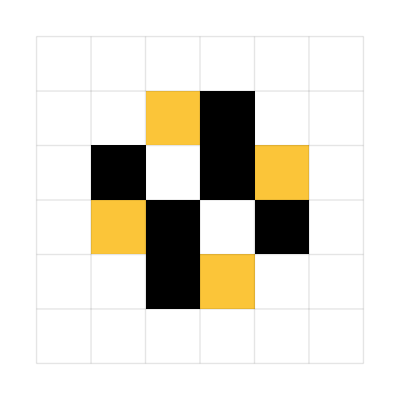
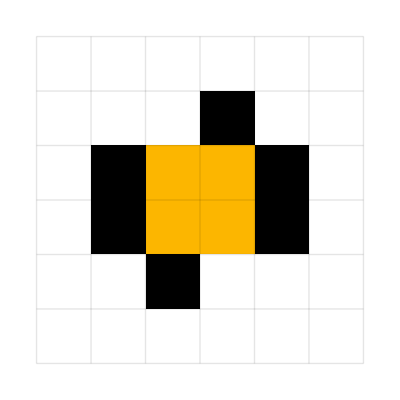
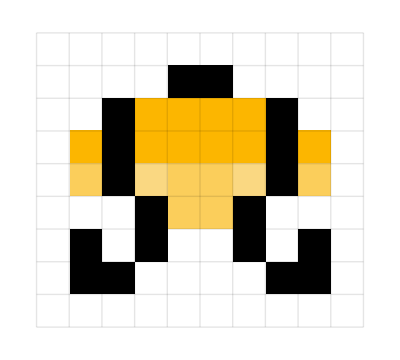
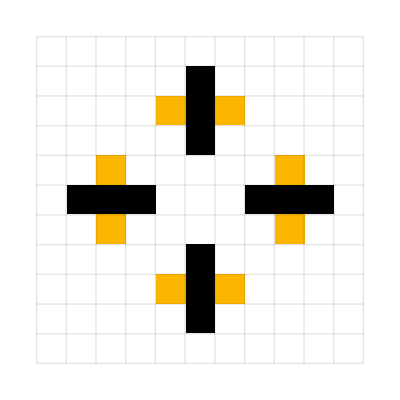
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
t10 = CellularAutomatonHistoryPlot["GameOfLife", {#[[-1]], 0}, 2Length[#]]&/@Values[$LifeParts["Oscillator"]][[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 10]]]
```

### Osc dependency matrix and frequencies

Matrix of all oscillator dependencies

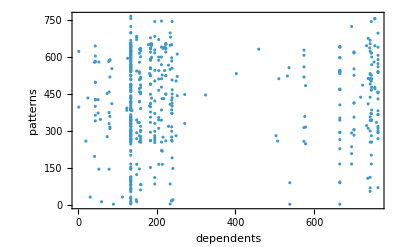

```mathematica
ListPlot[diffs, Frame-> True, FrameLabel->{"dependents", "patterns"}]
```

Winner take-all effects

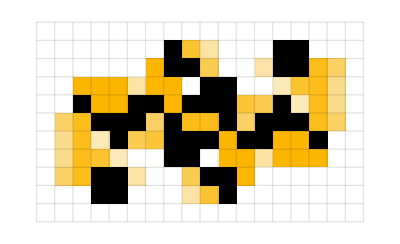
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
t10 = CellularAutomatonHistoryPlot["GameOfLife", {#[[-1]], 0}, 2Length[#]]&/@Values[$LifeParts["Oscillator"]][[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 20]]]
```

```mathematica
With[{tots = ReverseSort[Total/@ mat]},
ListLogLogPlot[ReplacePart[tots,Table[i-> Callout[tots[[i]], t10[[i]]], {i, 1, 20}]], Frame-> True, FrameLabel->{"oscillator", "frequency (log)"} ]
 ]
```

-Graphics-

#### How are these guys used?

```mathematica
ArrayPlot/@Values[$LifeParts["Oscillator"]][[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 20][[2]]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 20]
```

{134,184,665,762,159,742,195,156,745,238,44,223,239,701,149,205,212,746,81,234}

```mathematica
used = CellularAutomatonHistoryPlot["GameOfLife", {#[[-1]], 0}, Length[#]]&/@Values[$LifeParts["Oscillator"]][[Catenate[Position[mat[[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 20][[2]]]], 1]]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Bug?

```mathematica
ArrayPlot[{{1, 0, 1}, {0, 1, 0}}]
```

-Graphics-

```mathematica
ArrayPlot[ReplacePart[matdiff, 184->Table[Red, Length[matdiff]]], Frame->True, FrameTicks-> True]
```

-Graphics-

```mathematica
Catenate[Position[mat[[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 20][[2]]]], 1]]
```

{152,184,260,262,295,335,356,377,398,410,412,449,489,491,524,525,553,554,555,556,587,589,590,592,620,633,634,637,651,652,653,678}

```mathematica
GraphicsGrid[Partition[ArrayPlot[#, ImageSize->30]&/@Values[$LifeParts["Oscillator"]][[#]], 5]]&/@Catenate[Position[mat[[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 20][[2]]]], 1]][[;;10]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Using names

```mathematica
Keys[$LifeParts["Oscillator"]][[Catenate[Position[mat[[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 20][[2]]]], 1]]]]
```

{Charity's p16,Figure eight,p104lumpsofmuckshuttle,p104rpentominohassler,p120rpentominohassler,p144uturnerhassler,p16centuryhassler,p224 lumps of muck hassler,p280 U-turner hassler,p32 blinker hassler 2,p32 honey farm hassler,p40honeyfarmhassler,p48prepulsarshuttle,p48 toad hassler,p56c2honeyfarmhassler,p56honeyfarmhassler,p64honeyfarmhassler,p64honeyfarmhassler2,p64rpentominohassler2,p64 thunderbird hassler,p72centurylomhassler,p72honeyfarmhassler2,p72lumpsofmuckhassler,p72 quasi-shuttle,p80procrastinatorhassler,p88lumpsofmuckhassler,p88lumpsofmuckhassler2,p88rpentominoshuttle,p96 honey farm hassler,p96honeyfarmhassler2,p96honeyfarmhassler3,prepulsarshuttle40}

```mathematica
CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[#]]&/@ Keys[$LifeParts["Oscillator"]][[Catenate[Position[mat[[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 20][[2]]]], 1]]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Osc to guns?

### All instead of just osc

```mathematica
mat=Boole[Outer[SubsetQ[#2,#1]&,
Values[$LifeParts["Oscillator"]],
Values[$LifeParts["Oscillator"]],
1]];
```

```mathematica
Length[Values[$LifeParts["Oscillator"]]]
```

768

```mathematica
Total[Length/@Values[$LifeParts["Oscillator"]]]
```

53516

```mathematica
Keys[$LifeParts]
```

{Oscillator,Spaceship,Strict still life,Gun,Puffer,Induction coil,Reflector}

```mathematica
Total[Length/@Values[$LifeParts[#]]]&/@Keys[$LifeParts]
```

{53516,5019,169,7605,14737,630,506}

```mathematica
aps = Catenate[Values[$LifeParts[#]]&/@ Keys[$LifeParts]];
```

```mathematica
Length[aps]
```

1161

```mathematica
aps =Select[ Catenate[Values[$LifeParts[#]]&/@ Keys[$LifeParts]], Length[#]<300&& Times@@Dimensions[#[[-1]]]<=1000&];
```

```mathematica
Length[aps]
```

979

```mathematica
Map[Times@@Dimensions[#]&,aps, {2}]
```

```mathematica
Catenate[Map[Times@@Dimensions[#]&,aps, {2}]] // Histogram
```

-Graphics-

```mathematica
mat=Boole[Outer[SubsetQ[#2,#1]&,
aps,
aps,
1]];
```

```mathematica
Length[Catenate[aps]]
```

82182

```mathematica
Histogram[Length/@aps]
```

-Graphics-

```mathematica
Select[aps, ]
```

```mathematica
Count[aps, a_/;Times@@Dimensions[a]>= 1000, {2}]
```

745

```mathematica
Outer[f, {1, 2, 3}, {1, 2, 3}]
```

{{f[1,1],f[1,2],f[1,3]},{f[2,1],f[2,2],f[2,3]},{f[3,1],f[3,2],f[3,3]}}

#### V3

```mathematica
aps =Select[ Catenate[Values[$LifeParts[#]]&/@ Keys[$LifeParts]], Length[#]<300&& Times@@Dimensions[#[[-1]]]<=1000&];
```

```mathematica
matall = ParallelTable[Boole[SubsetQ[aps[[j]], aps[[i]]]],  {i, 1, Length[aps]}, {j,1, Length[aps]}];
```

$Aborted

This takes too long, need AWS

```mathematica
Table[f[i, j], {i, 1, 3}, {j, 1, 3}]
```

{{f[1,1],f[1,2],f[1,3]},{f[2,1],f[2,2],f[2,3]},{f[3,1],f[3,2],f[3,3]}}

### Dependency highlight

```mathematica
all = Join[Sequence@@Values[$LifeParts]];
```

```mathematica
allmat=Boole[Outer[SubsetQ[#2,#1]&,
Values[all],
Values[all],
1]];
```

$Aborted

```mathematica
overlap = Select[Position[mat, 1], #[[1]] != #[[2]]&];
```

```mathematica
names = Map[Keys[all][[#]]&, overlap, {2}];
```

```mathematica
Iconize[names]
```

```mathematica
HighlightGraph[#[[2]], 
VertexList[#[[2]]][[
(Function[{left, right},With[{common=Intersection[left,right]},{Flatten[Position[left,#]&/@common],Flatten[Position[right,#]&/@common]}]]@@
(Map[
(SparseArray[
Thread[
(Transpose[{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#[[-1]] ]]+ 1)->1]]&), 
VertexList/@ #, {2}]))[[2]]]]]&/@ Map[BoundingBoxLayeredGraph[$LifeData[#]]&, names[[{1}]], {2}]
```

{-Graphics-}

```mathematica
HighlightGraph[#[[2]], 
VertexList[#[[2]]][[
(Function[{left, right},With[{common=Intersection[left,right]},{Flatten[Position[left,#]&/@common],Flatten[Position[right,#]&/@common]}]]@@
(Map[
(SparseArray[
Thread[
(Transpose[{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#[[-1]] ]]+ 1)->1]]&), 
VertexList/@ #, {2}]))[[2]]]]]&/@ Map[BoundingBoxLayeredGraph[$LifeData[#]]&, names[[{1}]], {2}]
```

{-Graphics-}